```mathematica
Clear["Global`*"]
```

定义矩阵

```mathematica
d=12;
```

```mathematica
h[kx_,ky_]:=({{0, 0, 0, 0, 0, 0, 1, -ⅇ^(-ⅈ kx), 1/2, -1/2 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -(√3)/2, 1/2 √3 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)), 0, 0}, {0, 0, 0, 0, 0, 0, -ⅇ^(-ⅈ kx), 1, 0, 0, 1/2, -1/2 ⅇ^(-ⅈ (kx/2+(√3 ky)/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√3)/2, -1/2 √3 ⅇ^(-ⅈ (kx/2+(√3 ky)/2))}, {0, 0, 0, 0, 0, 0, 0, 0, -1/2 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)), 1/2, -1/2 ⅇ^(-ⅈ (kx/2+(√3 ky)/2)), 1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 1/2 √3 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)), -(√3)/2, -1/2 √3 ⅇ^(-ⅈ (kx/2+(√3 ky)/2)), (√3)/2}, {1, 0, -ⅇ^(ⅈ kx), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-ⅇ^(ⅈ kx), 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/2, -(√3)/2, 0, 0, -1/2 ⅇ^(1/2 ⅈ (kx-√3 ky)), 1/2 √3 ⅇ^(1/2 ⅈ (kx-√3 ky)), 0, 0, 0, 0, 0, 0}, {-1/2 ⅇ^(1/2 ⅈ (kx-√3 ky)), 1/2 √3 ⅇ^(1/2 ⅈ (kx-√3 ky)), 0, 0, 1/2, -(√3)/2, 0, 0, 0, 0, 0, 0}, {0, 0, 1/2, (√3)/2, -1/2 ⅇ^(1/2 ⅈ (kx+√3 ky)), -1/2 √3 ⅇ^(1/2 ⅈ (kx+√3 ky)), 0, 0, 0, 0, 0, 0}, {0, 0, -1/2 ⅇ^(1/2 ⅈ (kx+√3 ky)), -1/2 √3 ⅇ^(1/2 ⅈ (kx+√3 ky)), 1/2, (√3)/2, 0, 0, 0, 0, 0, 0}})+41*IdentityMatrix[d]
```

定义特征值特征向量函数

```mathematica
eva[kx_,ky_]:=Eigenvalues[h[kx,ky]]-41;
```

```mathematica
eve[kx_,ky_]:=Eigenvectors[h[kx,ky]];
```

```mathematica
deX[kx_,ky_]:=D[h[kx,ky],kx]//Evaluate
```

```mathematica
deY[kx_,ky_]:=D[h[kx,ky],ky]//Evaluate
```

```mathematica
derivativeX=Compile[{{kx,_Real},{ky,_Real}},D[h[kx,ky],kx]//Evaluate]
```

CompiledFunction[…]

```mathematica
derivativeY=Compile[{{kx,_Real},{ky,_Real}},D[h[kx,ky],ky]//Evaluate]
```

CompiledFunction[…]

定义贝里曲率函数

```mathematica
bc[kx_,ky_,n1_]:=-2*Im[Sum[If[n1≠n2,(Normalize[Conjugate[eve[kx,ky][[n1]]]].deX[kx,ky].Normalize[eve[kx,ky][[n2]]]*Normalize[Conjugate[eve[kx,ky][[n2]]]].deY[kx,ky].Normalize[eve[kx,ky][[n1]]])/(eva[kx,ky][[n1]]-eva[kx,ky][[n2]])^2,0],{n2,d}]]
```

```mathematica
bc[1.5,3.2,1]//Timing
```

{0.03125,-0.114531}

作图

```mathematica
c=1;
```

```mathematica
pointlist=Monitor[Table[c++;bc[kx//N,ky//N,1],{kx,-1.Pi,1.Pi,0.1},{ky,-1.Pi,1.Pi,0.1}],ProgressIndicator[c,{1,3950}]];
```

$Aborted

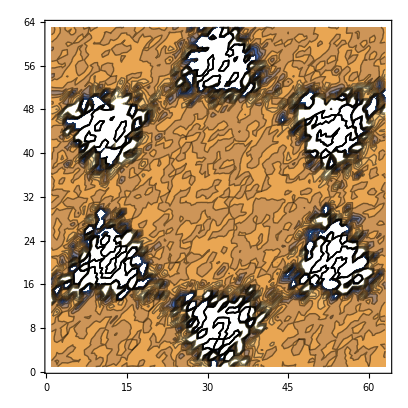

```mathematica
ListContourPlot[pointlist]
```